Frank Hertz Experiment

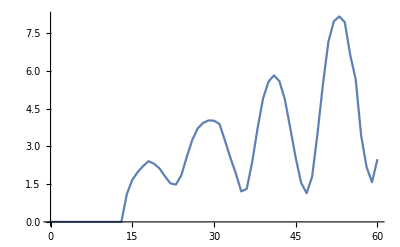

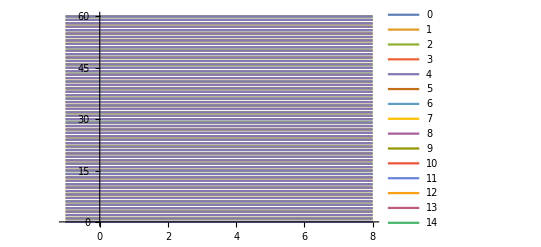

```mathematica
data = Import ["/home/jithin/codes/genlab-experiments/Frank Hertz/dataset.csv","CSV"];
voltage = data[[All,1]];
current = data[[All,2]];
plot = Transpose@{voltage,current};
ListLinePlot[plot]
max=First@FindMaximum[{voltage,-1≤x≤8},x];
min=First@FindMinimum[{voltage,-1≤x≤8},x];
Plot[{voltage,voltage''[x],max,min},{x,-1,8},PlotLegends->"Expressions"]
```